```mathematica
<<Notation`
Symbolize[Subscript[x_, y_]]
```

```mathematica
ClearAll[Subscript[θ, L],T,G,J]

Subscript[r, 1]=44/2 10^-3 ; (*meters*)
Subscript[r, 2]=60/2 10^-3 ; (*meters*)
Subscript[r, 3]=30/2 10^-3; (*meters*)

Subscript[J, 1]=(π ((Subscript[r, 2])^4-(Subscript[r, 1])^4))/2 (*meters^4*);
Subscript[J, 2]=(π (Subscript[r, 2])^4)/2 (*meters^4*);
Subscript[J, 3]=(π (Subscript[r, 3])^4)/2 (*meters^4*);

ClearAll[J]
J[X_]:=Piecewise[
{{Subscript[J, 1],0≤ X<0.6},
{Subscript[J, 2],0.6≤ X<0.8},
{Subscript[J, 3],0.8≤ X<1.2}}
] (*meters^4*)

T[X_]:=Piecewise[
{{2250,0≤ X<0.8},
{250,0.8≤ X<1.2}}
] (*meters^4*);

G[X_]:=Piecewise[
{{27  10^9,0≤ X<0.8}, (*Aluminum*)
{39 10^9,0.8≤ X<1.2}} (*Brass*)
] (*meters^4*);


L=1.2  (*in meters*);
```

```mathematica
Subscript[θ, L]=Integrate[T[X]/(J[X] G[X]),{X,0,1.2}] (*in radians*)
```

0.10063

```mathematica
Subscript[θ, L]/Degree (*in degrees*)
```

5.76567

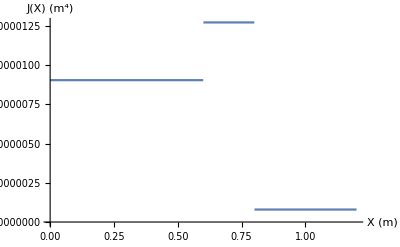

```mathematica
Plot[J[X],{X,0,1.2},AxesLabel->{"X (m)","J(X) (m^4)"}]
```

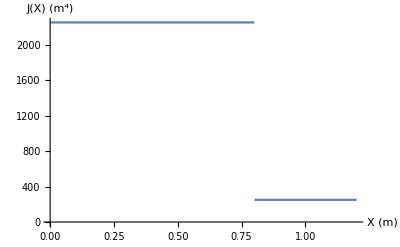

```mathematica
Plot[T[X],{X,0,1.2},AxesLabel->{"X (m)","J(X) (m^4)"}]
```

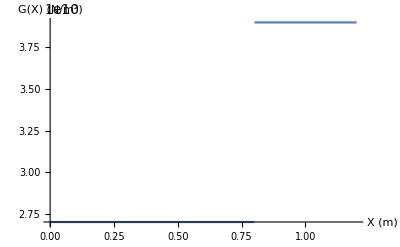

```mathematica
Plot[G[X],{X,0,1.2},AxesLabel->{"X (m)","G(X) (N/m^2)"}]
```